```mathematica
(************************Program Mahdi Molavi************************)
(********* git hub : https://github.com/mahdipc/mathematica*************)
```

```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
TrapStep[𝒻_,var_,{lowbound_,upperbound_}]:=Module[{ff=𝒻},
𝓃=15;
h=(upperbound-lowbound)/((*3𝓃*)𝓃-1);
Subscript[𝓍, ii_]=lowbound+ii h;
TH=h/2(ff/.var-> Subscript[𝓍, 0]+ff/.var-> Subscript[𝓍, 𝓃])+h Sum[(ff/.var-> Subscript[𝓍, i]),{i,1,𝓃}];
Return[TH];
];
J[τ_]:=Module[{},
Return[Piecewise[{{693/512(1-τ^2)^5,-1≤ τ && τ≤ 1}},0]];
];
k[ϵ_,s_,t_]:=Module[{},
Return[TrapStep[J[τ]k[s,t-ϵ τ],τ,{-1,1}]];
];
a[J_,ϵ_,s_]:=Module[{jj=J},
Return[TrapStep[kk[s,t]Cos[jj π t],t,{-1,1}]];
];
(************************************)
f[s_]=(1-1/(4 π^2))Sin[2 π s];
u[s_]=Sin[2π s];
k[s_,t_]=Piecewise[{{(1-s)t, 0≤ t≤ s≤ 1},{s(1-t), 0≤s<t≤ 1}},0];
Ν=10;
(************************************)
TimeObject[]
ϵ=N[Ν^(-4/5)];
kk[s_,t_]=k[ϵ,s,t];
aa[s_]=ParallelTable[Simplify[a[ji,ϵ,s]] ,{ji,0,Ν}];
```

18:11:10GMT+4.5TimeObject[{18,11,10.887122},TimeZone→4.5]

```mathematica
d=ParallelTable[∫_0^1 Cos[ji π s]f[s]ⅆs,{ji,0,Ν}];
```

```mathematica
A0=Table[1/2 TrapStep[Round[aa[ss]⟦1⟧ Cos[ji  π ss],10^-4],ss,{0,1}],{ji,0,Ν}]
```

{331/8000,0,-103/8000,0,-949/280000,0,-459/280000,0,-293/280000,0,-219/280000}

```mathematica
AI=Table[TrapStep[Round[aa[st]⟦ji+1⟧Cos[ji2 π st],10^-4],st,{0,1}],{ji,1,Ν},{ji2,0,Ν}];
```

```mathematica
A=Join[{A0},AI];
X=Inverse[IdentityMatrix[Ν+1]-A].d;
```

```mathematica
U[s_]:=1/2 X⟦1⟧aa[s]⟦1⟧+∑_(ji=2)^(Ν+1) X⟦ji⟧aa[s]⟦ji⟧+f[s];
US=Table[U[s],{s,0,1,0.05}]
```

{0.,0.304999,0.580207,0.798496,0.93848,0.986792,0.938531,0.79823,0.579934,0.304975,1.06963×10^-16,-0.304975,-0.579934,-0.79823,-0.938531,-0.986792,-0.93848,-0.798496,-0.580207,-0.304999,-2.28624×10^-16}

0.0132075

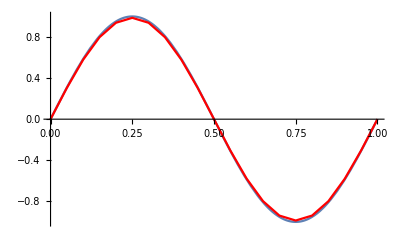

18:11:38GMT+4.5TimeObject[{18,11,38.480946},TimeZone→4.5]

```mathematica
Norm[Table[US⟦s+1⟧-u[s*0.05],{s,0,Length[US]-1}],Infinity]/Norm[Table[u[s*0.05],{s,0,Length[US]-1}],Infinity]
Show[Plot[u[s],{s,0,1}],ListLinePlot[Table[{s*0.05,US⟦s+1⟧},{s,0,Length[US]-1}],PlotStyle->{Red}]]
TimeObject[]
```